## Space Filling Curves

```mathematica
Manipulate[Graphics[c[n]],{n,1,5,1},{c,{HilbertCurve,PeanoCurve,SierpinskiCurve,KochCurve}},ControlType->Automatic]
```

```mathematica
fractals=EntityList[LinguisticAssistant];
LinguisticAssistant["Properties"]
```

{alternate names,associated entities,associated people,basic definitions,figure,long definition,MathWorld subject classifications,MSC 2010,name,related topics,related Wolfram Language symbols,definition,URL}

```mathematica
fractals[[1]][EntityProperty["MathWorld","URL"]]
```

```mathematica
fractalFigures=Image/@DeleteCases[#[EntityProperty["MathWorld","Diagram"]]&/@fractals,_Missing]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ConvertToRaster[img_]:=EdgeDetect[Binarize[img]]
```

```mathematica
FillDelta[rastor_]:=Table[{1/size,Total[Sign/@(Total[#,2]&/@(ImageData/@Flatten[ImagePartition[rastor,size]]))]},{size,10,Floor[Min[ImageDimensions[rastor]]/2]/2,10}]
```

```mathematica
Slope[delta_]:=Fit[Log[delta],{1,x},x][Slope]
```

```mathematica
FractalDimension[image_]:=image//ConvertToRaster//FillDelta//Slope
```

```mathematica
Entity["MathWorld","Fractal"]
```

fractal

```mathematica
FractalDimension[fractals[[1]]]
```

Binarize::imginv: Expecting an image or graphics instead of ….

EdgeDetect::imginv: Expecting an image or graphics instead of ….

ImageDimensions::imginv: Expecting an image or graphics instead of ….

Table::iterb: Iterator {size,10,1/2 Floor[1/2 ImageDimensions[EdgeDetect[Binarize[Failure[«2»]]]]],10} does not have appropriate bounds.

General::ivar: 2 is not a valid variable.

Fit[Log[Table[{1/size,Total[Sign/@(Total[#1,2]&)/@ImageData/@Flatten[ImagePartition[EdgeDetect[Binarize[Failure[…]]],size]]]},{size,10,1/2 Floor[1/2 ImageDimensions[EdgeDetect[Binarize[Failure[…]]]]],10}]],{1,2},2][Slope]

```mathematica
ConvertToRaster[img_]:=EdgeDetect[Binarize[img]]
```

```mathematica
fractalData=<|-Graphics-->0.6309,-Graphics-->1,-Graphics-->1.0812,-Graphics-->1.0933,-Graphics-->1.12915,-Graphics-->1.2,-Graphics-->1.2083,-Graphics-->1.2108,-Graphics-->1.2619,-Graphics-->1.2619,-Graphics-->1.2619,-Graphics-->1.2683,-Graphics-->1.328,-Graphics-->1.3057,-Graphics-->1.3934,-Graphics-->1.4649,-Graphics-->1.4649,-Graphics-->1.5,-Graphics-->1.5,-Graphics-->1.5236,-Graphics-->1.5849,-Graphics-->1.61803,-Graphics-->1.6379,-Graphics-->1.6667,-Graphics-->1.7,-Graphics-->1.7227,-Graphics-->1.7712,-Graphics-->1.7848,-Graphics-->1.8687,-Graphics-->1.8617,-Graphics-->1.8928,-Graphics-->1.974,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->1.9340|>;
```

```mathematica
fractalData=KeyMap[ConvertToRaster,fractalData];
```

```mathematica
fractalData=Normal[fractalData];
```

```mathematica
fractalData=RandomSample[fractalData];
```

```mathematica
training=fractalData[[5;;]];
test=fractalData[[;;4]]
```

{-Graphics-→1.6379,-Graphics-→1.974,-Graphics-→1.5849,-Graphics-→1.2683}

```mathematica
p=Predict[List@@training]
```

PredictorFunction[…]

```mathematica
p/@Keys[test]
```

{1.54831,1.60204,1.72387,1.56543}

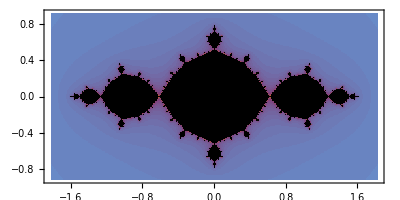
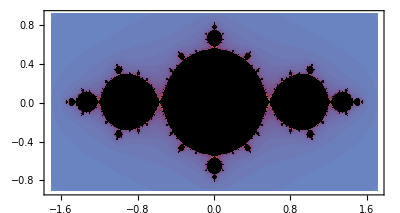
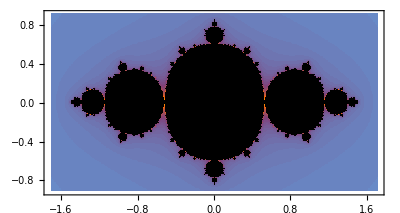
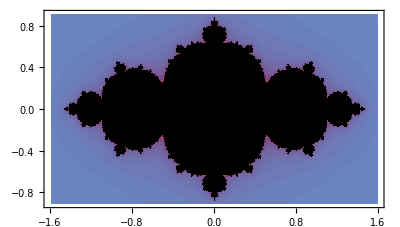
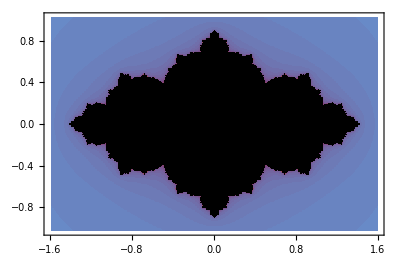
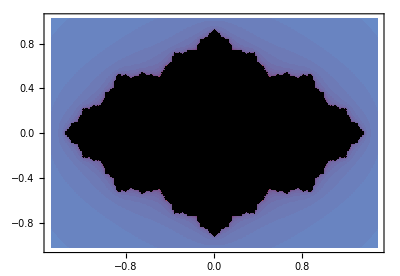
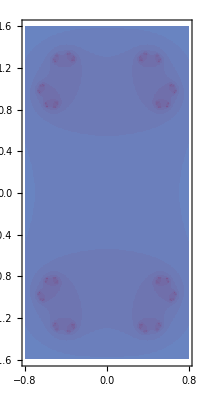
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
JuliaSetPlot/@Range[-1,1,0.1]
```

```mathematica
Table[JuliaSetPlot[RandomComplex[]],20]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
JuliaFractalDimension[c_]:=1+Abs[c]^2/4 Log[2]
```

```mathematica
MandelbrotSetPlot[]
```

-Graphics-

#### Sources

http://mathworld.wolfram.com/JuliaSet.html